```mathematica
<<logisticRegression`
```

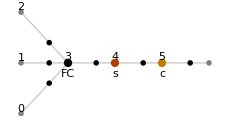
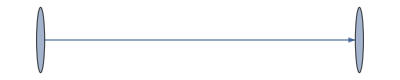
{NetChain[<>],0.256572,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{
net=NetInitialize@NetChain[{1,LogisticSigmoid},
"Input"->2,"Output"->NetDecoder["Scalar"]],net[{1,1}],NetInformation[net,"MXNetNodeGraphPlot"],NetInformation[net,"SummaryGraphic"],NetInformation[net,"LayersGraph"]}
```

## data

```mathematica
m=2.3;b=-5.85;
left=Cases[square,{x_,y_}/; EuclideanDistance[{x,y},{8,2}]<4];
right=Cases[square,{x_,y_}/; EuclideanDistance[{x,y},{0.5,10}]<5];data3=((#->0)&/@left)~Join~((#->1)&/@right);
```

## plot func

```mathematica
nett[{x_,y_}]:=x
```

```mathematica
plotSolution[net_,t_]:=Overlay[{
underneath=Rotate[ArrayPlot[Table[net[{x,y}],{x,0,10},{y,0,10}],Frame->False,ColorRules->{0->Gray,1->White}],π/2],
Show[Plot[m x+b,{x,0,10},PlotRange->{{0,10},{0,10}},PlotTheme->"Detailed",PlotStyle->{Red,Thickness[.02]},AspectRatio->1],
ListPlot[left,PlotStyle->Green,AspectRatio->1],
ListPlot[right,PlotStyle->Red,AspectRatio->1]]
}
];
```

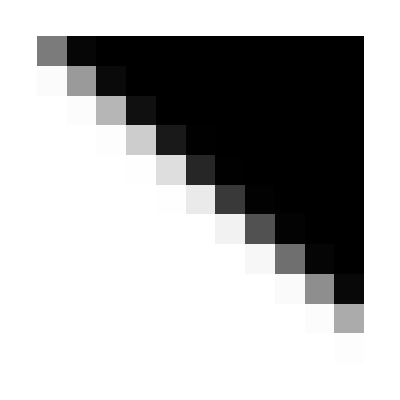
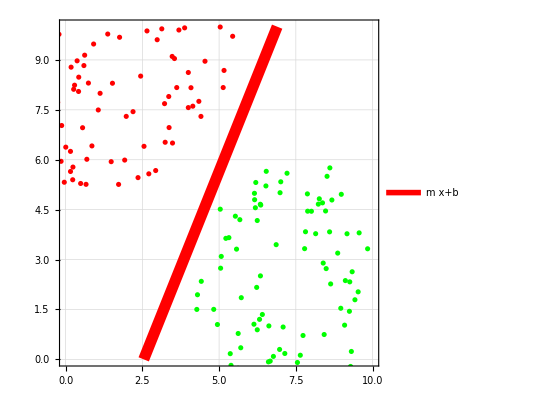

```mathematica
trained=NetTrain[net,data3,MaxTrainingRounds->Quantity[20,"Seconds"],Method->{"SGD","LearningRate"->0.1},TargetDevice->{"GPU",3},TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.01}];
plotSolution[trained,1]
```

```mathematica
gradientNorms[assoc_]:=BarChart[Log[Max[Abs[#]]]&/@assoc,ChartLabels->Automatic,BarOrigin->Right];
```

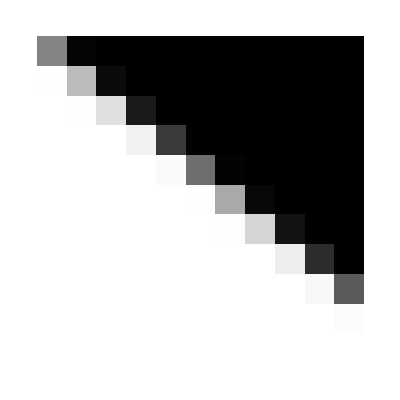
-Graphics--Graphics-

```mathematica
trained=NetTrain[net,data3,MaxTrainingRounds->Quantity[40,"Seconds"],Method->{"SGD","LearningRate"->0.1},TargetDevice->{"GPU",3},TrainingProgressReporting->{Function[#],"Interval"->Quantity[.5,"Seconds"]}];
plotSolution[trained,1]
```